## Meta-settings

```mathematica
$Version
```

```mathematica
Charting`ResolvePlotTheme[Automatic,VectorPlot];
vcf=ColorDataFunction[…];
```

```mathematica
Monitor`NestList[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
(*WFQTransit[weights_List,relaxation_:0]:=Function[state,RandomChoice[weights:>((#+state)&/@(IdentityMatrix[Length]~Join~(-IdentityMatrix[Length[state]])))]]*)
```

### Test for Изжо Лю

```mathematica
n=4;
Normal@SparseArray[{{i_,j_}/;j>i:>ⅇ^(-ⅈ*π/4)},{n,n}];
mat=%+%†+IdentityMatrix[n];
Clear[n]
mat//MatrixForm
PositiveSemidefiniteMatrixQ@mat
```

(1 | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | 1 | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | 1 | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | 1)

False

## Soft transitter

### Basic Idea

```mathematica
ComplexPlot3D[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z)),{z,0*(1+ ⅈ),2ⅇ*(1+ ⅈ)},ColorFunction->(Hue[2.95*(#8+0.5)]&),PlotLegends->BarLegend["Rainbow"],PlotRange->All,Mesh->Full]
```

-Graphics3D-

```mathematica
Simplify[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z))/.z->(a+ⅈ b)]/.{Im[a]->0,Im[b]->0,Re[a]->a,Re[b]->b,Re[a+b]->a+b}
%//Expand
```

(1+ⅈ) ⅇ^(-a-b) (-1-ⅈ ⅇ^a+ⅈ ⅇ^b+ⅇ^(a+b))

(1+ⅈ)-(1-ⅈ) ⅇ^-a-(1+ⅈ) ⅇ^(-a-b)+(1-ⅈ) ⅇ^-b

### Visualization of the softness

```mathematica
Manipulate[VectorPlot[-{(1-ⅇ^(-x/n0))(1+ⅇ^(-y/n0)),(1+ⅇ^(-x/n0))(1-ⅇ^(-y/n0))},{x,0,5},{y,0,5}, VectorPoints->Tuples[Range[0,5],2],VectorMarkers->"Drop",VectorScaling->Automatic,VectorRange->All,VectorColorFunction->(vcf[#5/2]&),VectorColorFunctionScaling->False,PlotLegends->BarLegend[{(vcf[#/2]&),{0,2}}],Epilog->{vcf[0],Point[{0,0}]}],{{n0,1},0.1,20}]
```

```mathematica
Manipulate[VectorPlot3D[-{(1+ⅇ^(-y/n0)+ⅇ^(-z/n0))(1-ⅇ^(-x/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-z/n0))(1-ⅇ^(-y/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-y/n0))(1-ⅇ^(-z/n0))},{x,0,3},{y,0,3},{z,0,3}, VectorPoints->Tuples[Range[0,3],3]],{{n0,1},0.0001,5}]
```

## Time-regime simulation

### Verification of Convergence

```mathematica
Transit[n_,n0_:1]:=RandomChoice[{1,2(1-ⅇ^(-n/n0))}:>{n+1,n-1}]
myhist[ls_]:=BarChart[MeanAround/@(Transpose@PadRight[(HistogramList/@Partition[ls,Floor[Sqrt[Length[ls]]]])⟦All,2⟧,Automatic,""]/.""->Nothing),BarSpacing->None]
```

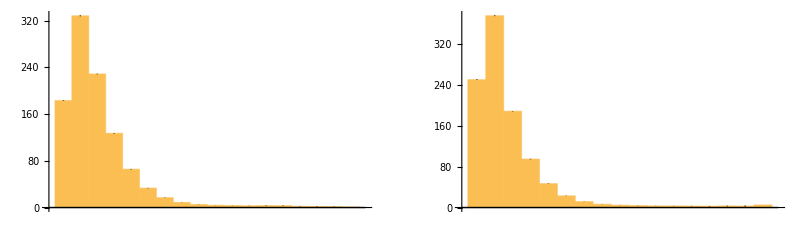

```mathematica
ls1=Monitor`NestList[Transit[#,1]&,0,1000000]//Quiet;
ls0=Monitor`NestList[Transit[#,0.001]&,0,1000000]//Quiet;
GraphicsRow[{myhist[ls1],myhist[ls0]}]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=nestListWithMonitor[Transit[#,1]&,{0,0},10000000]//Quiet;
```

### Simulations

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=nestListWithMonitor[Transit[#,1]&,{0,0},10000000]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1+ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=nestListWithMonitor[Transit[#,0.01]&,{0,0},10000000]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=nestListWithMonitor[Transit[#,1]&,{0,0},10]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

Histogram3D::ldata: nestListWithMonitor[Transit[#1,1]&,{0,0},10] is not a valid dataset or list of datasets.

Histogram3D[nestListWithMonitor[Transit[#1,1]&,{0,0},10],ColorFunction→TemperatureMap]

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=nestListWithMonitor[Transit[#,0.01]&,{0,0},10000000]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Binomial-Poisson entropic inequalities and the M/M/∞ queueBinomial-Poisson entropic inequalities and the M/M/∞ queue
```

## New stuff